## Load function

```mathematica
(* Linux *)
link = Install[NotebookDirectory[]<>"bin/MathematicaPEntropy"]
```

LinkObject[…]

```mathematica
(* Windows *)
link = Install[NotebookDirectory[]<>"x64\\Mathematica\\Pentropy"]
```

LinkObject[…]

## Permutation entropy for random sequence

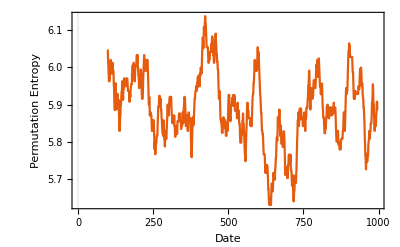

```mathematica
rand = RandomReal[{0,1},1000];
dates = Range[1000];
pentropy = PermutationEntropy[dates,rand,5,100];
ListLinePlot[pentropy, PlotTheme->"Scientific", FrameLabel->{"Date", "Permutation Entropy"}]
```

## Permutation entropy for deterministic sequence and random sequence

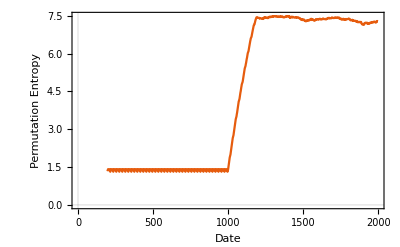

```mathematica
constant = Table[Mod[i,20],{i,1,1000}];
rand = RandomReal[{0,1},1000];
num = Join[constant,rand];
dates = Range[2000];
pentropy = PermutationEntropy[dates,num,6,200];
ListLinePlot[pentropy, PlotTheme->"Scientific", FrameLabel->{"Date", "Permutation Entropy"}]
```